# Crossing Point Geometry

## [Tyr-((OH⋯OH)_2(H_2 O))_2] - e^- ⟶ [TyrO^•((⋯HOH)_2(H_2 O))_2]^+

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/souda/Documents/Projects/Kevin-Zhu/PCET-rate-Tyr-water/geometries

## Useful Functions

```mathematica
GamessXYZ[mol_]:=Module[{al,out},al=AtomList[Molecule[mol],All,{"AtomicNumber","AtomCoordinates"}];
out=QuantityMagnitude/@Flatten/@al[[First/@Molecule[mol]["SymmetryEquivalentAtoms"]]];
out/. z_Integer:>Sequence[ElementData[z,"Abbreviation"],z]];
```

```mathematica
XYZcoords[mol_]:=QuantityMagnitude@mol["AtomCoordinates"];
```

## Preliminaries

### Range of proton donor-acceptor distances

```mathematica
listRDA=Range[2.77,2.77]
```

{2.77}

```mathematica
nRDA=Length[listRDA]
```

1

```mathematica
iD=10;
iH=11;
iA=16;
```

### Read reactant and product optimized geometries for all DA distances from XYZ files

“Molecule” objects:

```mathematica
reactantStructure=Table[Import["r_R"<>ToString[listRDA[[i]]]<>".xyz"],{i,1,nRDA}];
productStructure=Table[Import["p_R"<>ToString[listRDA[[i]]]<>".xyz"],{i,1,nRDA}];
```

```mathematica
BondList[productStructure[[1]]]
```

{Bond[{1,2},Single],Bond[{1,3},Single],Bond[{1,4},Single],Bond[{4,5},Single],Bond[{5,7},Double],Bond[{7,8},Single],Bond[{7,9},Single],Bond[{9,10},Double],Bond[{9,12},Single],Bond[{12,14},Double],Bond[{14,15},Single],Bond[{12,13},Single],Bond[{5,6},Single],Bond[{1,19},Single],Bond[{11,16},Single],Bond[{16,18},Single],Bond[{20,21},Single],Bond[{20,22},Single],Bond[{23,24},Single],Bond[{23,25},Single],Bond[{14,4},Single]}

```mathematica
productStructure=Map[MoleculeModify[#,{"ReplaceAtom",16->Atom["O","Valence"->3]},ValenceErrorHandling->False]&,productStructure]
```

{Molecule[…]}

```mathematica
productStructure=Map[MoleculeModify[#,{"AddBond",Bond[{16,17},"Single"]},ValenceErrorHandling->False]&,productStructure]
```

Molecule::valenc: Invalid valence for oxygen atom at position 16.

{Molecule[…]}

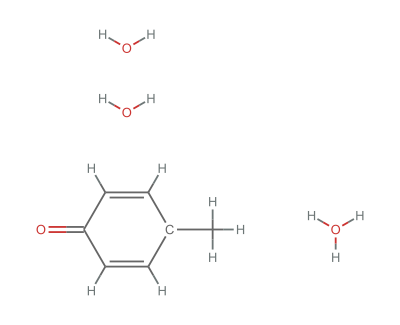

```mathematica
MoleculePlot[productStructure[[1]],PlotTheme->"AllAtom"]
```

```mathematica
MoleculePlot3D[productStructure[[1]],
PlotTheme->"BallAndStick",
AtomLabels->"AtomIndex",
AxesLabel->{"x","y","z"},
AxesStyle->Directive[Thickness[Large],Magenta,24],
Ticks->None,ImageSize->Large]
```

MoleculePlot3D[Molecule[…],PlotTheme→BallAndStick,AtomLabels→AtomIndex,AxesLabel→{x,y,z},AxesStyle→Directive[Thickness[Large],RGBColor[1, 0, 1],24],Ticks→None,ImageSize→Large]

Move the origin to the middle of the D-A bond

```mathematica
productStructure[[1]]
```

Molecule[…]

```mathematica
MoleculeModify[reactantStructure[[1]],{"TransformAtomCoordinates",TranslationTransform[-(XYZcoords[reactantStructure[[1]]][[iD]]+XYZcoords[reactantStructure[[1]]][[iA]])/2]}]
```

MoleculeModify[Molecule[…],{TransformAtomCoordinates,TransformationFunction[(1. | 0. | 0. | -38.8234
0. | 1. | 0. | -28.314
0. | 0. | 1. | -33.1086
0. | 0. | 0. | 1.)]}]

```mathematica
reactantStructure0=Map[MoleculeModify[#,{"TransformAtomCoordinates",TranslationTransform[-(XYZcoords[#][[iD]]+XYZcoords[#][[iA]])/2]}]&,reactantStructure];
productStructure0=Map[MoleculeModify[#,{"TransformAtomCoordinates",TranslationTransform[-(XYZcoords[#][[iD]]+XYZcoords[#][[iA]])/2]}]&,productStructure];
```

Part::partw: Part 10 of QuantityMagnitude[Missing[NotAvailable]] does not exist.

Part::partw: Part 16 of QuantityMagnitude[Missing[NotAvailable]] does not exist.

```mathematica
productStructure[[1]]
```

Molecule[…]

Remove the transferring hydrogen from all structures (last atom):

```mathematica
reactantStructureNoH=Map[MoleculeModify[#,{"DeleteAtom",iH}]&,reactantStructure];
productStructureNoH=Map[MoleculeModify[#,{"DeleteAtom",iH}]&,productStructure];
iA+=-1;
```

```mathematica
reactantStructure[[1]]
```

Molecule[…]

```mathematica
MoleculePlot3D[productStructure[[1]],
PlotTheme->"BallAndStick",
AtomLabels->{Atom[Except["H"]]->"AtomIndex"},
Axes->True,AxesOrigin->{0,0,0},
AxesLabel->{"x","y","z"},
AxesStyle->Directive[Thickness[Large],Magenta,24],
Ticks->None,ImageSize->Large]
```

-Graphics3D-

```mathematica
MoleculePlot3D[productStructure[[1]],
PlotTheme->"BallAndStick",
AtomLabels->"AtomIndex",
AxesLabel->{"x","y","z"},
AxesStyle->Directive[Thickness[Large],Magenta,24],
Ticks->None,ImageSize->Large]
```

MoleculePlot3D[Molecule[…],PlotTheme→BallAndStick,AtomLabels→AtomIndex,AxesLabel→{x,y,z},AxesStyle→Directive[Thickness[Large],RGBColor[1, 0, 1],24],Ticks→None,ImageSize→Large]

```mathematica
Show[
MoleculePlot3D[reactantStructureNoH[[1]],ColorRules->{_->Blue}],
MoleculePlot3D[productStructureNoH[[1]],ColorRules->{_->Red}],
ImageSize->Large,
Axes->True,AxesOrigin->{0,0,0},
AxesLabel->{"x","y","z"},
AxesStyle->Directive[Thickness[Large],Dashed,Magenta,24],
Ticks->None
]
```

Show::gcomb: Could not combine the graphics objects in ….

Show[-Graphics3D-,MoleculePlot3D[Molecule[…],ColorRules→{_→RGBColor[1, 0, 0]}],ImageSize→Large,Axes→True,AxesOrigin→{0,0,0},AxesLabel→{x,y,z},AxesStyle→Directive[Thickness[Large],Dashing[{Small,Small}],RGBColor[1, 0, 1],24],Ticks→None]

Cartesian coordinates only:

```mathematica
reactantXYZ=Table[XYZcoords[reactantStructure[[i]]],{i,1,nRDA}];
productXYZ=Table[XYZcoords[productStructure[[i]]],{i,1,nRDA}];
reactantNoHXYZ=Table[XYZcoords[reactantStructureNoH[[i]]],{i,1,nRDA}];
productNoHXYZ=Table[XYZcoords[productStructureNoH[[i]]],{i,1,nRDA}];
```

```mathematica
productXYZ[[1]]
```

{{34.8667,31.1688,28.8932},{35.2125,31.7264,28.0206},{34.2334,31.835,29.4931},{36.0101,30.6564,29.7167},{35.7718,29.735,30.7738},{34.7543,29.403,30.9586},{36.7966,29.2641,31.5546},{36.6143,28.5605,32.3605},{38.1596,29.696,31.32},{39.1329,29.2836,32.022},{38.8398,28.157,33.3415},{38.3861,30.6314,30.2382},{39.4066,30.9535,30.0594},{37.339,31.0862,29.4728},{37.5232,31.7871,28.6642},{38.6567,27.5159,34.1008},{38.9045,27.9546,35.004},{39.1751,26.6334,33.954},{34.2258,30.3468,28.557},{39.8848,25.3397,33.6931},{40.7927,25.3489,34.0308},{39.4528,24.599,34.1437},{39.2415,28.5429,36.3385},{39.9594,29.1906,36.2809},{38.4909,29.0273,36.7133}}

Numbers of atoms in each structure (the same in most cases)

```mathematica
reactantNatoms=Table[AtomCount[reactantStructure[[i]]],{i,1,nRDA}];
productNatoms=Table[AtomCount[productStructure[[i]]],{i,1,nRDA}];
reactantNoHNatoms=Table[AtomCount[reactantStructureNoH[[i]]],{i,1,nRDA}]
productNoHNatoms=Table[AtomCount[productStructureNoH[[i]]],{i,1,nRDA}]
```

{24}

{24}

Lists with the contents of files in XYZ format:

```mathematica
reactantXYZfile=Table[Join[{{reactantNatoms[[i]]},{"Reactant state optimized geometry with constraint DA distance R = "<>ToString[listRDA[[i]]]<>" Å"}},MapAt[Flatten[#]&,MapAt[QuantityMagnitude[#]&,AtomList[reactantStructure[[i]],_,{"AtomicSymbol","AtomCoordinates"}],{All,2}],{All}]],{i,1,nRDA}];
productXYZfile=Table[Join[{{productNatoms[[i]]},{"Product state optimized geometry with constraint DA distance R = "<>ToString[listRDA[[i]]]<>" Å"}},MapAt[Flatten[#]&,MapAt[QuantityMagnitude[#]&,AtomList[productStructure[[i]],_,{"AtomicSymbol","AtomCoordinates"}],{All,2}],{All}]],{i,1,nRDA}];
reactantNoHXYZfile=Table[Join[{{reactantNoHNatoms[[i]]},{"Reactant state optimized geometry with constraint DA distance R = "<>ToString[listRDA[[i]]]<>" Å (no H)"}},MapAt[Flatten[#]&,MapAt[QuantityMagnitude[#]&,AtomList[reactantStructureNoH[[i]],_,{"AtomicSymbol","AtomCoordinates"}],{All,2}],{All}]],{i,1,nRDA}];
productNoHXYZfile=Table[Join[{{productNoHNatoms[[i]]},{"Product state optimized geometry with constraint DA distance R = "<>ToString[listRDA[[i]]]<>" Å (no H)"}},MapAt[Flatten[#]&,MapAt[QuantityMagnitude[#]&,AtomList[productStructureNoH[[i]],_,{"AtomicSymbol","AtomCoordinates"}],{All,2}],{All}]],{i,1,nRDA}];
```

```mathematica
Export["tmp5_manual.xyz",reactantXYZfile[[5]],"Table"];
```

```mathematica
productNoHXYZfile[[1]]
```

{{24},{Product state optimized geometry with constraint DA distance R = 2.77 Å (no H)},{C,34.8667,31.1688,28.8932},{H,35.2125,31.7264,28.0206},{H,34.2334,31.835,29.4931},{C,36.0101,30.6564,29.7167},{C,35.7718,29.735,30.7738},{H,34.7543,29.403,30.9586},{C,36.7966,29.2641,31.5546},{H,36.6143,28.5605,32.3605},{C,38.1596,29.696,31.32},{O,39.1329,29.2836,32.022},{C,38.3861,30.6314,30.2382},{H,39.4066,30.9535,30.0594},{C,37.339,31.0862,29.4728},{H,37.5232,31.7871,28.6642},{O,38.6567,27.5159,34.1008},{H,38.9045,27.9546,35.004},{H,39.1751,26.6334,33.954},{H,34.2258,30.3468,28.557},{O,39.8848,25.3397,33.6931},{H,40.7927,25.3489,34.0308},{H,39.4528,24.599,34.1437},{O,39.2415,28.5429,36.3385},{H,39.9594,29.1906,36.2809},{H,38.4909,29.0273,36.7133}}

## Alignment/Averaging procedure

```mathematica
(*
molR - reactant molecule object (obtained from importing a XYZ file);
molP - product molecule object (obtained from importing a XYZ file);
alignmentN - number of atoms defining "heavy" parts of the molecules which will be aligned first (starting from atom 1);
iA, iB, iC, iD - four atom indices defining the torsion angle for "light" parts of the milecules, with iC-iD being the acceptor-donor pair.
*)
RPaverage[molR_,molP_,alignmentN_,iA_,iB_,iC_,iD_]:=Module[
{i,alignmentMap,molPaligned,molPaveraged,molRaveraged, torsionAngles,θ,molRaveragedRotated,molPaveragedRotated,avVector,avVectoriD,molRaveragedRotatedX,molPaveragedRotatedX,molAveraged,xyzC,xyzD,xyzDShifted,molAveragedShifted,molAveragedFinal},

(* align heaviest parts of the molecules defined by alignmentMap *)
alignmentMap=Table[i->i,{i,1,alignmentN}];
molPaligned=MoleculeAlign[molR,molP,alignmentMap];

(* Average coordinates of the heaviest parts of the molecules *)
molPaveraged=molPaligned;
For[i=1,i<alignmentN+1,i++,
molPaveraged=MoleculeModify[molPaveraged,{"SetAtomPosition",i->(XYZcoords[molR][[i]]+XYZcoords[molPaligned][[i]])/2}]
];
(* adjust the remaining of the molecule R so that the DA distance would remain the same in R and P average structures *)
For[i=alignmentN+1,i<AtomCount[molPaveraged]+1,i++,
molPaveraged=MoleculeModify[molPaveraged,{"SetAtomPosition",i->XYZcoords[molPaveraged][[i]]+XYZcoords[molPaveraged][[iC]]-XYZcoords[molPaligned][[iC]]}]
];
molRaveraged=molR;
For[i=1,i<alignmentN+1,i++,
molRaveraged=MoleculeModify[molRaveraged,{"SetAtomPosition",i->XYZcoords[molPaveraged][[i]]}]
];
(* adjust the remaining of the molecule R so that the DA distance would remain the same in R and P average structures *)
For[i=alignmentN+1,i<AtomCount[molRaveraged]+1,i++,
molRaveraged=MoleculeModify[molRaveraged,{"SetAtomPosition",i->XYZcoords[molRaveraged][[i]]+XYZcoords[molRaveraged][[iC]]-XYZcoords[molR][[iC]]}]
];

(* Set the atom iB at the origin of the coordinate system *)
molRaveraged=MoleculeModify[molRaveraged,{"TransformAtomCoordinates",TranslationTransform[-XYZcoords[molRaveraged][[iB]]]}];
molPaveraged=MoleculeModify[molPaveraged,{"TransformAtomCoordinates",TranslationTransform[-XYZcoords[molPaveraged][[iB]]]}];

(* rotate to align iB-iC with the Z-axis *)
molRaveraged=MoleculeModify[molRaveraged,{"TransformAtomCoordinates",RotationTransform[{XYZcoords[molRaveraged][[iC]],{0,0,1}}]}];
molPaveraged=MoleculeModify[molPaveraged,{"TransformAtomCoordinates",RotationTransform[{XYZcoords[molPaveraged][[iC]],{0,0,1}}]}];

(* calculate torsion angles iA-iB-iC-iD in the reactant and product molecules after initial algnment and averaging *)
(* and then calculate average tosion angle Θ *)
torsionAngles={MoleculeValue[molRaveraged,{"TorsionAngle",{iA,iB,iC,iD}}],MoleculeValue[molPaveraged,{"TorsionAngle",{iA,iB,iC,iD}}]};
θ=Mean[torsionAngles]-torsionAngles[[1]];

(* rotate both reactant and product "light" parts around iB-iC axis towards each other using ± average torsion angle θ *)
molRaveragedRotated=MoleculeModify[molRaveraged,{"TransformAtomCoordinates",RotationTransform[θ,XYZcoords[molRaveraged][[iC]]-XYZcoords[molRaveraged][[iB]]]}];
molPaveragedRotated=MoleculeModify[molPaveraged,{"TransformAtomCoordinates",RotationTransform[-θ,XYZcoords[molPaveraged][[iC]]-XYZcoords[molPaveraged][[iB]]]}];
For[i=1,i<alignmentN+1,i++,
molRaveragedRotated=MoleculeModify[molRaveragedRotated,{"SetAtomPosition",i->XYZcoords[molRaveraged][[i]]}];
molPaveragedRotated=MoleculeModify[molPaveragedRotated,{"SetAtomPosition",i->XYZcoords[molPaveraged][[i]]}]
];

(* Now do two hopefully very small rotations to align donor atoms iD midway *)
avVector=XYZcoords[molRaveragedRotated][[iD]]-XYZcoords[molRaveragedRotated][[iC]]+XYZcoords[molPaveragedRotated][[iD]]-XYZcoords[molPaveragedRotated][[iC]];
avVectoriD=avVector/Norm[avVector] Norm[XYZcoords[molRaveragedRotated][[iD]]-XYZcoords[molRaveragedRotated][[iC]]];
molRaveragedRotatedX=MoleculeModify[molRaveragedRotated,{"TransformAtomCoordinates",RotationTransform[{XYZcoords[molRaveragedRotated][[iD]]-XYZcoords[molRaveragedRotated][[iC]],avVectoriD},XYZcoords[molRaveragedRotated][[iC]]]}];
molPaveragedRotatedX=MoleculeModify[molPaveragedRotated,{"TransformAtomCoordinates",RotationTransform[{XYZcoords[molPaveragedRotated][[iD]]-XYZcoords[molPaveragedRotated][[iC]],avVectoriD},XYZcoords[molPaveragedRotated][[iC]]]}];
For[i=1,i<alignmentN+1,i++,
molRaveragedRotatedX=MoleculeModify[molRaveragedRotatedX,{"SetAtomPosition",i->XYZcoords[molRaveragedRotated][[i]]}];
molPaveragedRotatedX=MoleculeModify[molPaveragedRotatedX,{"SetAtomPosition",i->XYZcoords[molPaveragedRotated][[i]]}]
];

(* do final averaging of the manipulated R and P structures *)
molAveraged=molRaveragedRotatedX;
For[i=alignmentN+1,i<AtomCount[molAveraged]+1,i++,
molAveraged=MoleculeModify[molAveraged,{"SetAtomPosition",i->(XYZcoords[molRaveragedRotatedX][[i]]+XYZcoords[molPaveragedRotatedX][[i]])/2}]
];

(* Now set the center to the middle od the iC-iD (acceptor-donor) axis and orient iC-iD along the Z-axis *)
(*
xyzC=XYZcoords[molAveraged][[iC]];
xyzD=XYZcoords[molAveraged][[iD]];
molAveragedShifted=MoleculeModify[molAveraged,{"TransformAtomCoordinates",TranslationTransform[-(xyzC+xyzD)/2]}];
xyzDShifted=XYZcoords[molAveragedShifted][[iD]];
molAveragedFinal=MoleculeModify[molAveragedShifted,{"TransformAtomCoordinates",RotationTransform[{xyzDShifted,{0,0,1}}]}];
*)

molAveraged
];
```

```mathematica
molR=reactantStructureNoH[[1]];
molP=productStructureNoH[[1]];
```

```mathematica
molX=MoleculeAlign[molR,molP]
```

MoleculeAlign::sbst: Could not generate automatic atom mapping = provide an explicit atom mapping or a MoleculePattern.

MoleculeAlign[Molecule[…],Molecule[…]]

```mathematica
molAveragedX=RPaverage[molR,molP,22,9,10,15,22]
```

Part::partw: Part 15 of … does not exist.

MoleculeModify::mol: Argument … is not a valid molecule.

Part::partw: Part 15 of … does not exist.

MoleculeModify::mol: Argument … is not a valid molecule.

MoleculeValue::mol: Argument … is not a valid molecule.

Part::partw: Part 15 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

MoleculeModify::mol: Argument … is not a valid molecule.

General::stop: Further output of MoleculeModify::mol will be suppressed during this calculation.

AtomCount::mol: Argument MoleculeModify[MoleculeModify[MoleculeModify[MoleculeModify[MoleculeModify[<<14>>[<<2>>], {<<2>>}], {<<2>>}], {<<2>>}], {<<2>>}], {<<2>>}] is not a valid molecule.

$Aborted

```mathematica
XYZcoords[molAveragedX][[10]]
```

{1.54843,0.315862,3.52961}

```mathematica
MoleculeValue[molAveragedX,{"BondLength",{10,15}}]
```

MoleculeValue::mol: Argument MoleculeModify[MoleculeModify[MoleculeModify[MoleculeModify[MoleculeModify[<<14>>[<<2>>], {<<2>>}], {<<2>>}], {<<2>>}], {<<2>>}], {<<2>>}] is not a valid molecule.

$Aborted

```mathematica
Show[
MoleculePlot3D[molAveragedX,
PlotTheme->"BallAndStick",
AtomLabels->None,
Axes->True,AxesOrigin->{0,0,0},
AxesLabel->{"x","y","z"},ImageSize->Large,
AxesStyle->Arrowheads[0.1],
Ticks->None],
Graphics3D[{Magenta,Arrowheads[0.05],Arrow[Tube[{{0,0,0},{0,0,5}},0.075]]}]
]
```

-Graphics3D-

```mathematica
Chop@XYZcoords[molAveragedX]
```

{{0,0,0},{-1.21065,1.73629,-0.0140441},{1.39394,1.44895,0.0883057},{1.78125,-1.1375,-0.0611823},{-2.55052,1.79667,-0.0859382},{-3.24252,3.00444,-0.0561481},{-2.51818,4.18964,0.0488768},{-1.12701,4.1336,0.122929},{-0.486885,2.89561,0.0915692},{1.89357,-2.47205,-0.169157},{3.12793,-3.11569,-0.181161},{4.28555,-2.34806,-0.0802951},{4.17582,-0.962254,0.0283257},{2.91321,-0.371376,0.034698},{0.981824,2.7338,0.159959},{1.92884,3.75327,0.281795},{3.2812,3.40931,0.32488},{3.67832,2.0737,0.248663},{2.69516,1.08778,0.130805},{-3.07124,0.849625,-0.166247},{-4.32486,3.00285,-0.114891},{-3.02468,5.14903,0.0719903},{-0.548128,5.04598,0.201309},{0.967733,-3.02963,-0.242878},{3.16762,-4.19574,-0.267013},{5.26404,-2.81704,-0.0869134},{5.06473,-0.348364,0.105267},{1.62698,4.79182,0.342987},{4.03066,4.18814,0.418484},{4.7293,1.81254,0.280452},{-1.45889,-1.51723,-0.183959},{-0.186148,-0.173394,-2.07756},{-2.03544,-2.16681,0.841213},{-1.70545,-1.88277,1.83253},{-2.9928,-3.15737,0.651145},{-3.43125,-3.65661,1.50725},{-3.36685,-3.49173,-0.651718},{-2.76585,-2.82028,-1.71864},{-3.03725,-3.06485,-2.7379},{-1.32917,-1.26948,-3.87939},{-2.06214,-1.98703,-4.22622},{-0.606021,-0.524343,-4.80887},{0.338782,0.397328,-4.34664},{0.933939,0.998189,-5.02521},{0.514874,0.543617,-2.97712},{1.23447,1.2508,-2.58361},{-1.80928,-1.83647,-1.46091},{-1.10341,-1.08279,-2.51295},{0,0,2.08662},{-0.90581,-0.798436,-6.58054},{-1.92227,-1.85227,-6.84395},{-1.22601,0.705795,-7.04838},{0.542722,-1.04449,-7.25355},{-1.37251,0.785723,-8.01113},{0.767114,-1.99246,-7.30996},{-4.62417,-4.7759,-0.914265},{-5.18038,-5.31921,0.34259},{-5.69922,-4.15929,-1.92811},{-3.82032,-5.76463,-1.8704},{-6.44156,-3.7454,-1.4698},{-4.35799,-6.5193,-2.17239},{1.54843,0.315862,3.52961},{2.07626,-0.529385,3.44589},{2.20168,1.06235,3.64343},{-0.827798,0.265154,2.48502},{2.92936,-1.96692,3.25282},{3.27629,2.36088,3.76515},{2.58383,-2.54296,3.37519},{3.39765,-2.05247,3.70537},{3.33617,2.6012,4.70317},{2.82543,3.11896,3.36337}}

```mathematica
tmp=MoleculeModify[molAveragedX,"CanonicalizeAtomCoordinates"];
xyzC=Chop@XYZcoords[tmp][[49]];
xyzD=Chop@XYZcoords[tmp][[62]];
xyzCD=(xyzC+xyzD)/2
MoleculeModify[tmp,{"TransformAtomCoordinates",TranslationTransform[{-30,0,0.5}]}]
```

{3.19115,2.40981,-0.243962}

Molecule[…]

```mathematica
Show[
MoleculePlot3D[tmp,
PlotTheme->"BallAndStick",
AtomLabels->None,
Axes->True,AxesOrigin->{0,0,0},
AxesLabel->{"x","y","z"},ImageSize->Large,
AxesStyle->Arrowheads[0.1],
Ticks->None],
Graphics3D[{Magenta,Arrowheads[0.05],Arrow[Tube[{{0,0,0},{0,0,5}},0.075]]}]
]
```

-Graphics3D-

## Averaging for all DA distances

```mathematica
averageStructureNoH=Table[RPaverage[reactantStructureNoH[[i]],productStructureNoH[[i]],61,2,1,49,62],{i,1,nRDA}];
```

```mathematica
averageNoHXYZfile=Table[Join[{{AtomCount[averageStructureNoH[[i]]]},{"Average geometry (no active H) with constraint DA distance R = "<>ToString[listRDA[[i]]]<>" Å"}},MapAt[Flatten[#]&,MapAt[QuantityMagnitude[#]&,AtomList[averageStructureNoH[[i]],_,{"AtomicSymbol","AtomCoordinates"}],{All,2}],{All}]],{i,1,nRDA}];
```

```mathematica
averageNoHXYZfile[[1]]
```

{{71},{Average geometry (no active H) with constraint DA distance R = 2.14 Å},{Ru,0.,0.,0.},{N,-1.21065,1.73629,-0.0140441},{N,1.39394,1.44895,0.0883057},{N,1.78125,-1.1375,-0.0611823},{C,-2.55052,1.79667,-0.0859382},{C,-3.24252,3.00444,-0.0561481},{C,-2.51818,4.18964,0.0488768},{C,-1.12701,4.1336,0.122929},{C,-0.486885,2.89561,0.0915692},{C,1.89357,-2.47205,-0.169157},{C,3.12793,-3.11569,-0.181161},{C,4.28555,-2.34806,-0.0802951},{C,4.17582,-0.962254,0.0283257},{C,2.91321,-0.371376,0.034698},{C,0.981824,2.7338,0.159959},{C,1.92884,3.75327,0.281795},{C,3.2812,3.40931,0.32488},{C,3.67832,2.0737,0.248663},{C,2.69516,1.08778,0.130805},{H,-3.07124,0.849625,-0.166247},{H,-4.32486,3.00285,-0.114891},{H,-3.02468,5.14903,0.0719903},{H,-0.548128,5.04598,0.201309},{H,0.967733,-3.02963,-0.242878},{H,3.16762,-4.19574,-0.267013},{H,5.26404,-2.81704,-0.0869134},{H,5.06473,-0.348364,0.105267},{H,1.62698,4.79182,0.342987},{H,4.03066,4.18814,0.418484},{H,4.7293,1.81254,0.280452},{N,-1.45889,-1.51723,-0.183959},{N,-0.186148,-0.173394,-2.07756},{C,-2.03544,-2.16681,0.841213},{H,-1.70545,-1.88277,1.83253},{C,-2.9928,-3.15737,0.651145},{H,-3.43125,-3.65661,1.50725},{C,-3.36685,-3.49173,-0.651718},{C,-2.76585,-2.82028,-1.71864},{H,-3.03725,-3.06485,-2.7379},{C,-1.32917,-1.26948,-3.87939},{H,-2.06214,-1.98703,-4.22622},{C,-0.606021,-0.524343,-4.80887},{C,0.338782,0.397328,-4.34664},{H,0.933939,0.998189,-5.02521},{C,0.514874,0.543617,-2.97712},{H,1.23447,1.2508,-2.58361},{C,-1.80928,-1.83647,-1.46091},{C,-1.10341,-1.08279,-2.51295},{O,1.38778×10^-17,-6.93889×10^-18,2.08662},{P,-0.90581,-0.798436,-6.58054},{O,-1.92227,-1.85227,-6.84395},{O,-1.22601,0.705795,-7.04838},{O,0.542722,-1.04449,-7.25355},{H,-1.37251,0.785723,-8.01113},{H,0.767114,-1.99246,-7.30996},{P,-4.62417,-4.7759,-0.914265},{O,-5.18038,-5.31921,0.34259},{O,-5.69922,-4.15929,-1.92811},{O,-3.82032,-5.76463,-1.8704},{H,-6.44156,-3.7454,-1.4698},{H,-4.35799,-6.5193,-2.17239},{O,1.54843,0.315862,3.52961},{H,2.07626,-0.529385,3.44589},{H,2.20168,1.06235,3.64343},{H,-0.827798,0.265154,2.48502},{O,2.92936,-1.96692,3.25282},{O,3.27629,2.36088,3.76515},{H,2.58383,-2.54296,3.37519},{H,3.39765,-2.05247,3.70537},{H,3.33617,2.6012,4.70317},{H,2.82543,3.11896,3.36337}}

```mathematica
Do[
Export["Ru_R"<>ToString[listRDA[[i]]]<>"00_averaged.xyz",averageNoHXYZfile[[i]],"Table"],
{i,1,nRDA}];
```

Add Hydrogen atom next to the donor oxygen (Hright) and next to the acceptor oxygen (Hleft):

```mathematica
Block[{OdonorXYZ,OacceptorXYZ,HleftXYZ,HrightXYZ,HleftXYZfile,HrightXYZfile},
Do[
OdonorXYZ=XYZcoords[averageStructureNoH[[i]]][[62]];
OacceptorXYZ=XYZcoords[averageStructureNoH[[i]]][[49]];
HleftXYZ=OacceptorXYZ+(OdonorXYZ-OacceptorXYZ)/Norm[OdonorXYZ-OacceptorXYZ]×0.95;
HrightXYZ=OdonorXYZ-(OdonorXYZ-OacceptorXYZ)/Norm[OdonorXYZ-OacceptorXYZ]×0.95;
HleftXYZfile=
Join[
{
{AtomCount[averageStructureNoH[[i]]]+1},
{"Average geometry (with H left) with constraint DA distance R = "<>ToString[listRDA[[i]]]<>" Å"}
},
MapAt[Flatten[#]&,MapAt[QuantityMagnitude[#]&,AtomList[averageStructureNoH[[i]],_,{"AtomicSymbol","AtomCoordinates"}],{All,2}],{All}],
{Flatten[{{"H",HleftXYZ}}]},
{{" "}}
];
HrightXYZfile=
Join[
{
{AtomCount[averageStructureNoH[[i]]]+1},
{"Average geometry (with H right) with constraint DA distance R = "<>ToString[listRDA[[i]]]<>" Å"}
},
MapAt[Flatten[#]&,MapAt[QuantityMagnitude[#]&,AtomList[averageStructureNoH[[i]],_,{"AtomicSymbol","AtomCoordinates"}],{All,2}],{All}],
{Flatten[{"H",HrightXYZ}]},
{{" "}}
];
Export["Ru_R"<>ToString[listRDA[[i]]]<>"00_aver-Hleft.xyz",HleftXYZfile,"Table"];
Export["Ru_R"<>ToString[listRDA[[i]]]<>"00_aver-Hright.xyz",HrightXYZfile,"Table"],
{i,1,nRDA}]
];
```